# DFT 学习 - 从信号采样出发

## 信号采样

### 假设有某段时间的有k个周期的sin信号的n个采样点 先来写个这样的函数

```mathematica
signData[k_,n_,φ_:0]:=Table[Sin[k 2π(t-1)/n+φ],{t,n}]
signData2[k_,n_,φ_:0]:=Sin[k 2π#/n+φ]&/@Range[0,n-1]
signData3[k_,n_,φ_:0]:=Sin/@(k Subdivide[2π,n][[;;n]]+φ)
signData33[k_,n_,φ_:0]:=Sin/@(k Subdivide[2π,n][[;;-2]]+φ)
```

上面的表达式都是等价的

```mathematica
Grid@Table[sd[2,10,π/3],{sd,{signData,signData2,signData3,signData33}}]
```

(√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15] | (√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15]
(√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15] | (√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15]
(√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15] | (√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15]
(√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15] | (√3)/2 | Cos[(7 π)/30] | -Sin[(2 π)/15] | -Cos[π/30] | -Sin[π/15]

### 再结合上一步写个绘制采样信号的函数

```mathematica
sg[k_,n_,φ_:0]:=Block[{sd,pts,lines},sd=Table[Sin[k 2π(r-1)/n+φ],{r,n}];
(*pts=Table[{r-1,sd[[r]]},{r,n}];*)
lines=Chop@Table[{{r-1,0},{r-1,sd[[r]]}},{r,n}];Graphics[{{Line@lines},{Magenta,PointSize[Medium],Point@lines[[All,2]](*pts*)}},Axes->True,AxesOrigin->{0,0},AspectRatio->0.5,PlotLabel->StringForm["k=``, φ=``",k,φ],
GridLines->Automatic,GridLinesStyle->Directive[Orange, Dotted]]]
```

```mathematica
sg1[k_,n_,φ_:0]:=DiscretePlot[Chop@Evaluate@Sin[2π k x/n+φ],{x,0,n-1},
PlotLabel->StringForm["k=``, φ=``",k,φ],PlotStyle->Directive[Magenta],
GridLines->Automatic,GridLinesStyle->Directive[Orange, Dotted]]
```

### 交互式观察不同周期和采样对应的图形

```mathematica
Manipulate[sg[k,n,φ],{{k,2,"周期"},0,n,1},{{n,20,"采样"},Max[k,10],50,1},{{φ,0,"初相"},0,2π}]
```

### 对照观察各频率采样，Floor[n/2]等价于Ceiling[(n-1)/2]

```mathematica
Manipulate[Grid@Table[{sg[k,n],sg[n-k,n],sg[k,n,ϕ]},{k,0,Floor[n/2]}],{{n,10,"采样"},10,20,1},{{ϕ,0,"初相"},0,2π},SaveDefinitions->True]
```

### 貌似具有某些对称性，比如周期为k和n-k的信号采样关于x轴对称，周期为k和周期也为k但初相为π的信号采样关于x轴对称。 其反应出一个现象，较高频率的采样和对应的较低频率移相π的采样是一样的， 也可以理解成：-sin(x)=sin(x±π)

## 信号相关性

```mathematica
Manipulate[Plot[{Sin[ka x+φa],Sin[kb x+φb],Sin[ka x+φa]Sin[kb x+φb]},{x,0,2π},
Filling->{3->Axis},PlotLegends->{"a","b","∫a*b"},
PlotLabel->StringForm["f=``",Chop@Integrate[Sin[ka x+φa]Sin[kb x+φb],{x,0,2π}]]],{ka,1,10,1},{φa,0,2π},{kb,1,10,1},{φb,0,2π}]
```

## 离散傅里叶变换

### 内置函数Fourier : 长度为 n 的一个列表 u_r 的离散傅里叶变换 v_s 在默认情况下定义为 1/(√n)∑_(r=1)^n u_r e^(2π i(r-1)(s-1)/n)

### 粗浅解释：离散傅里叶变换就是分别用周期数为0，1，2，3，...，n-2，n-1的基信号与原信号对比，计算方式为对应离散值相乘再相加，得到与该频率的相关性 但也要注意，后半部分有较高周期数的基信号应当理解为带有相位π的低频信号 这里我们并不关心时间，可以将周期数理解为频率

交互式计算信号采样的离散傅里叶变换

```mathematica
table[A_,ω_,φ_,b_,n_]:=Block[{f,len,p,q,l},l=Table[A Sin[ω 2π (r-1)/n+φ]+b,{r,n}];f=Chop@Fourier@l;len=Length@f;p=Ceiling[len/2];
q=Floor[len/2];{l,f,(Norm/@f)/√n,Arg/@f,Range[0,len-1],Range[-len,-1],Range[0,p-1]~Join~Range[p-len,-1],Range[0,q]~Join~Range[q-len+1,-1]}]

Manipulate[t=table[A,ω,φ,b,n];Grid[If[showIndex,t,t[[{1,2,3,-2,-1}]]],Frame->All],{{A,1,"振幅"},0.5,5},{{ω,2,"频率"},0,n,1},{{φ,0,"初相"},-π,π},{{b,0,"偏距"},-2,2},{{n,10,"采样"},Max[ω,10],20,1},{{showIndex,True,"索引"},{True->"显示",False->"隐藏"}}]
```

1：离散傅里叶变换的结果
2：结果的模
3：结果的辐角
4：索引-1，前半部分对应周期数(频率)
5：反向索引，后半部分对应负的(反向旋转)周期数(频率)
6：频率（周期）
7：频率（周期）

变换后的结果显示出某种对称性
每一项可以理解为关于某个频率信号的相关性
第一个频率为0，第二个频率为1，后面的频率一次加一
最后一个频率为-1，最后第二个频率为-2，依次递推
原因呢，就在上一节，较高频信号的采样结果会与有初相的低频信号一样

可以看到，频率（周期）为k和-k处是有值的，而且共轭，其余都为0
那么是不是离散傅里叶变换结果的一半就足以描述原信号了呢？

### 关于离散傅里叶变换结果

对于变换结果中某个频率的复数值，其模长表示振幅，辐角表示初相(相对余弦)

### 使用DFT还原信号

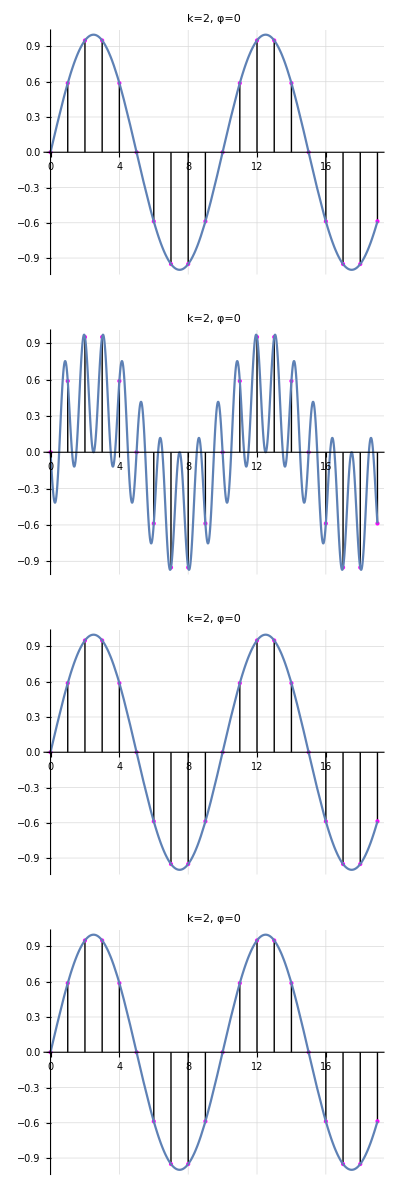

```mathematica
len=20;
f=Chop@Fourier@Table[Sin[2 2π(n-1)/len],{n,len}];p1=Plot[Sum[(2Norm[f[[n]]])/(√len)Cos[((n-1)2π)/len t-Arg[f[[n]]]],{n,len/2}],{t,0,len-1}];
p2=Plot[Sum[Norm[f[[n]]]/(√len)Cos[((n-1)2π)/len t-Arg[f[[n]]]],{n,len}],{t,0,len-1}];

p3=Plot[Sum[fn=f[[Mod[n+len,len]+1]]/√len;Norm[fn]Cos[(n 2π)/len t-Arg[fn]],{n,-5,4}],{t,0,len-1}];
p4=Plot[Sum[fn=f[[Mod[n+len,len]+1]]/√len;-Norm[fn]Cos[(n 2π)/len t+Arg[fn]],{n,-5,4}],{t,0,len-1}];

Column@Table[Show[sg[2,20],p,ImageSize->Medium],{p,{p1,p2,p3,p4}}]
```

### 包装成函数

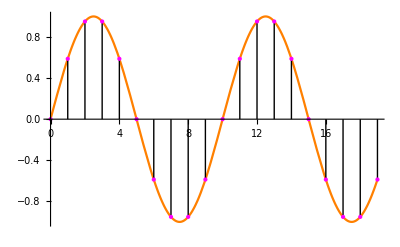

```mathematica
dftPlot[k_,n_,φ_:0]:=Block[{f=Chop@Fourier@signData[k,n,φ],func,p,c},p=Ceiling[n/2];func=Sum[c=f[[Mod[r+n,n]+1]]/√n;Norm[c]Cos[(2π r)/n x-Arg[c]],{r,p-n,p-1}];Show[Plot[func,{x,0,n-1},PlotStyle->Orange,PlotRange->All],sg[k,n,φ]]]

dftPlot[2,20]
```

```mathematica
Manipulate[dftPlot[ω,n,φ],{{ω,2,"频率"},0,n,1},{{φ,0,"初相"},-π,π},{{n,10,"采样"},Max[ω,10],50,1}]
```

### 好了到目前为止我们研究了对单一频率的信号采样计算DFT 后面我们再深入研究多个频率的信号复合时计算DFT